```mathematica
(*Nastavitev delovne mape na trenutno mapo*)
SetDirectory[NotebookDirectory[]];

(*Uvoz slik za klasifikator*)
izbrane=Import/@FileNames["*",FileNameJoin[{NotebookDirectory[],"Klasifikator_izbrane"}]];
zavrnjene=Import/@FileNames["*",FileNameJoin[{NotebookDirectory[],"Klasifikator_zavrnjene"}]];
```

```mathematica
(*Normalizacija slik na primerno velikost*)
resizeImage[img_]:=ImageResize[img,{256,256}];
izbraneSlike=Map[resizeImage, izbrane];
zavrnjeneSlike=Map[resizeImage, zavrnjene];
```

```mathematica
(*Označevanje slik*)
izbraneOznačene=Map[{#->"izbrana"}&,izbraneSlike];
zavrnjeneOznačene=Map[{#->"zavrnjena"}&,zavrnjeneSlike];
skupajKlasifikator=Flatten[Join[izbraneOznačene,zavrnjeneOznačene],1];
```

```mathematica
(*Priprava slik za validacijo*)
validacijaIzbrane =Import /@ FileNames["*",FileNameJoin[{NotebookDirectory[],"Validacija_izbrane"}]];
validacijaZavrnjene =Import /@ FileNames["*",FileNameJoin[{NotebookDirectory[],"Validacija_neizbrane"}]]; 
izbraneSlikeValidacija=Map[resizeImage, validacijaIzbrane];
zavrnjeneSlikeValidacija=Map[resizeImage, validacijaZavrnjene];

ValiIzbraneOznačene = Map[(#->"izbrana")& ,izbraneSlikeValidacija];
ValiZavrnjeneOznačene = Map[(#->"zavrnjena")& ,zavrnjeneSlikeValidacija];

validacija = Join[ValiZavrnjeneOznačene , ValiIzbraneOznačene];
```

```mathematica
(*Klasifajer*)
c = Classify[skupajKlasifikator, PerformanceGoal->"Quality",Method->"RandomForest",FeatureExtractor -> "ImageFeatures", ValidationSet->validacija]
```

ClassifierFunction[…]

```mathematica
(*Zaradi varčevanja s pomnilnikom, brisanje starih spremenljivk*)
ClearAll[validacijaIzbrane, validacijaZavrnjene, validacija, izbrane, zavrnjene, izbraneSlike, zavrnjeneSlike, izbraneSlikeValidacija, zavrnjeneSlikeValidacija, izbraneOznačene, zavrnjeneOznačene, skupajKlasifikator, ValiIzbraneOznačene, ValiZavrnjeneOznačene]
```

```mathematica
(*Priprava slik za testiranje*)
testIzbrane =Import /@ FileNames["*",FileNameJoin[{NotebookDirectory[],"Tesiranje_izbrane"}]];
testZavrnjene =Import /@ FileNames["*",FileNameJoin[{NotebookDirectory[],"Tesiranje_neizbrane"}]]; 

izbraneSlikeTest=Map[resizeImage, testIzbrane];
zavrnjeneSlikeTest=Map[resizeImage, testZavrnjene];

TestizbraneOznačene = Map[(#->"izbrana")& ,izbraneSlikeTest];
TestzavrnjeneOznačene = Map[(#->"zavrnjena")& ,zavrnjeneSlikeTest];

skupajPravilno = Join[TestizbraneOznačene , TestzavrnjeneOznačene];
```

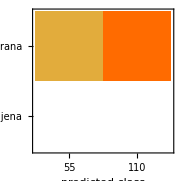
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 165
Accuracy | (33.4.) %
Accuracy baseline | (100.00000000000000022) %
Geometric mean of probabilities | 0.442 ± 0.0075
Mean cross entropy | 0.816 ± 0.017
Single evaluation time | 138. ms/example
Batch evaluation speed | 5.49 examples/s
-Graphics- |

{-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana,-Graphics-→izbrana}

0.333333

-Graphics-

```mathematica
(*Testiranje in prikaz natančnosti*)
cm = ClassifierMeasurements[c, skupajPravilno]
cm["Examples"]
cm["Accuracy"]
cm["ConfusionMatrixPlot"]
```